Poisson Process

Generate a sample of  n = 10  exponential random variables

```mathematica
$Line:=0;
```

```mathematica
SeedRandom[]
```

```mathematica
e1=Table[Random[PoissonDistribution[10]],{10}]   (* exponential ~ λ = 1 *)
```

{8,13,16,5,9,12,9,11,10,12}

```mathematica
Num=Length[e1]                        (* Length[list] = # elements in list *)
```

10

Create the first 10 arrival times of the Poisson Process including  0

```mathematica
s=FoldList[Plus,0,e1]
```

{0,0.468882,1.22499,1.60233,3.18415,5.4655,7.28644,7.3574,8.48767,9.43948,12.499}

Show a discrete plot of   (S_i, N(S_i) ) ,  S_i= arrival times,   i = 0, 1, . . . , Num

```mathematica
timeNumber=Table[{s[[i]],i-1},{i,1,Num+1}]
```

{{0,0},{0.468882,1},{1.22499,2},{1.60233,3},{3.18415,4},{5.4655,5},{7.28644,6},{7.3574,7},{8.48767,8},{9.43948,9},{12.499,10}}

```mathematica
??PlotStyle
```

PlotStyle is an option for plotting and related functions that specifies styles in which objects are to be drawn.

Attributes[PlotStyle]={Protected}

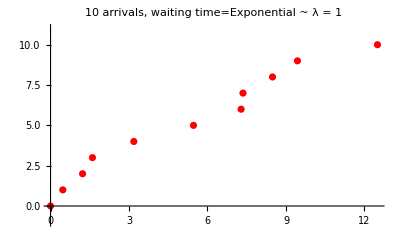

```mathematica
ListPlot[timeNumber,PlotStyle->Red,PlotRange->{Automatic,{-1,11}},AxesOrigin->{0,0},PlotLabel->"10 arrivals, waiting time=Exponential ~ λ = 1"]
```

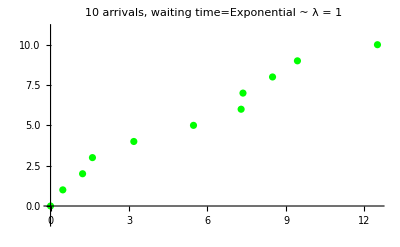

```mathematica
ListPlot[timeNumber,PlotStyle->Green, PlotStyle->PointSize[.02],PlotRange->{Automatic,{-1,11}},AxesOrigin->{0,0},PlotLabel->"10 arrivals, waiting time=Exponential ~ λ = 1"]
```

Show a continuous time plot  (s,  N(s) ) ,  0 ≤  s  ≤   S_(Num+1)+1

```mathematica
AppendTo[s,s[[Num+1]]+1]  (*  Subscript[S, Num+1] +1 added to list s *)
```

{0,0.468882,1.22499,1.60233,3.18415,5.4655,7.28644,7.3574,8.48767,9.43948,12.499,13.499}

```mathematica
Plotting by means of  Boole[ ] function
?Boole
```

Boole::argx: Boole called with 0 arguments; 1 argument is expected.

by function means of Plotting Boole[]

Boole[expr] yields 1 if expr is True and 0 if it is False.

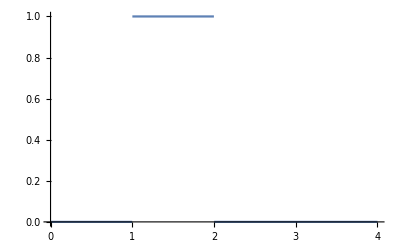

```mathematica
a=1;b=2;

Plot[Boole[a≤x<b],{x,0,4}]
```

```mathematica
f[x_]:=∑_(i=1)^(Num+1) ((i-1) Boole[s[[i]]≤x<s[[i+1]]])
```

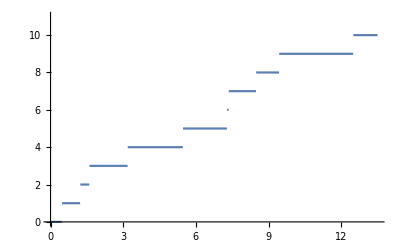

```mathematica
Plot[f[x],{x,0,s[[Num+1]]+1},PlotRange->{0,Num+1}]
```

```mathematica
Plotting by using Table[],Plot[], Show[]
```

The plotting option:   PlotRange→{{a, b},{c, d}}, gives the graph window for  a ≤ x ≤ b,  c ≤ y ≤ d

```mathematica
Table[f[x_]:=i-1/;s[[i]]≤x<s[[i+1]],{i,1,Num+1}];    (* defines f[] piece-wise as i-1  on the interval (s[[i]], s[[i+1]]] *)
```

```mathematica
graph=Table[Plot[f[x],{x,s[[i]],s[[i+1]]},PlotRange->{{0,s[[Num+1]]+1},{0,Num+1}},DisplayFunction->Identity],{i,1,Num+1}];
```

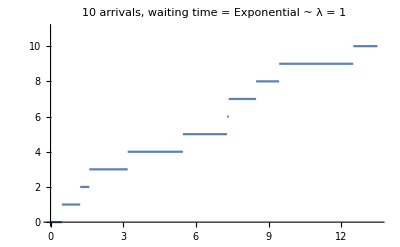

```mathematica
Show[graph,PlotLabel->"10 arrivals, waiting time = Exponential ~ λ = 1",DisplayFunction->$DisplayFunction]
```

Plot Option:   ' DisplayFunction → Identity '  delays display of  the graph until  ' DisplayFunction → $DisplayFunction '   
is called in the command  Show[ . ].

Another way to show Poisson sample as a staircase is to use the built-in  UnitStep[x] function

```mathematica
??UnitStep
```

RowBox[{"UnitStep", "[", StyleBox["x", "TI"], "]"}] represents the unit step function, equal to 0 for RowBox[{StyleBox["x", "TI"], "<", "0"}] and 1 for RowBox[{StyleBox["x", "TI"], "≥", "0"}]. 
RowBox[{"UnitStep", "[", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "]"}] represents the multidimensional unit step function which is 1 only if none of the SubscriptBox[StyleBox["x", "TI"], StyleBox["i", "TI"]] are negative.

Attributes[UnitStep]={Listable,NumericFunction,Orderless,Protected,ReadProtected}

The list  below holds 10 arrival times

```mathematica
??Piecewise
```

RowBox[{"Piecewise", "[", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["val", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["cond", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["val", "TI"], StyleBox["2", "TR"]], ",", SubscriptBox[StyleBox["cond", "TI"], StyleBox["2", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] represents a piecewise function with values SubscriptBox[StyleBox["val", "TI"], StyleBox["i", "TI"]] in the regions defined by the conditions SubscriptBox[StyleBox["cond", "TI"], StyleBox["i", "TI"]]. 
RowBox[{"Piecewise", "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["val", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["cond", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["val", "TI"]}], "]"}] uses default value StyleBox["val", "TI"] if none of the SubscriptBox[StyleBox["cond", "TI"], StyleBox["i", "TI"]] apply. The default for StyleBox["val", "TI"] is 0.

Attributes[Piecewise]={HoldAll,Protected,ReadProtected}
 
Piecewise/:Default[Piecewise,2]:=0

```mathematica
s=Drop[FoldList[Plus,0,Table[Random[ExponentialDistribution[1]],{10}]],1]
(* this generates parial sums of the exponential distribution, namely arrival times *)
```

{3.09084,3.36571,3.97131,4.12103,5.9738,7.62815,9.56011,11.8067,13.6016,16.1603}

```mathematica
PoissonSample[u_]:=∑_(i=1)^10 UnitStep[u-s[[i]]]
```

The graph of the sample for  0 ≤ u ≤ t =12

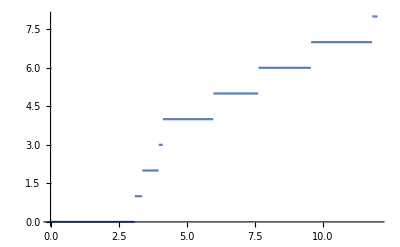

```mathematica
Plot[PoissonSample[u],{u,0,12}]
```

To sample Poisson Process on the interval [0, t] one has to keep adding exponential random variables  X_i (inter-arrival times), 
until their sum exceeds t  for the first time, i.e.,  X_1+...+X_N ≤ t  and X_(N+1) > t . Then N = N(t) = #  Poisson signals in [0, t].  

In other words, to simulate a sample path of Poisson Process on [0, t] one first needs to repeatedly simulate exponential variables 
to find N(t) and then use Num = N(t) for graphing purposes.

Generate a single sample of a Poisson Process N(t)  ~ λ on [0, t]

```mathematica
Clear[a,s,r,t,u,f,λ,Num]  
t=10;λ=1;s={};a=0;Label[start];r=Random[ExponentialDistribution[λ]]; a=a+r;  If[a≤t,AppendTo[s,a];Goto[start]];
```

```mathematica
s                       (* list s contains arrival times : < Subscript[S, 1]< Subscript[S, 2] < ... < Subscript[S, n]≤ t, Subscript[S, i]= Subscript[X, 1]+...+Subscript[X, i]*)
```

{0.0120315,1.00848,2.82661,3.58873,3.96024,4.04802,4.82088,9.46393}

```mathematica
Num=Length[s]                                      (* Length[a] = N(t) *)
```

8

Show a continuous time plot  (u,  N(u) ) ,  0 ≤ u ≤ t  for Poisson Process on [0, t]

```mathematica
PrependTo[s,0]; AppendTo[s,t];               (* add 0 and t to list s *)
s
```

{0,0.422843,1.92083,1.93132,2.04551,5.56954,5.85178,7.0429,7.41906,7.49451,8.01839,9.00623,10}

```mathematica
??Piecewise
```

RowBox[{"Piecewise", "[", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["val", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["cond", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["val", "TI"], StyleBox["2", "TR"]], ",", SubscriptBox[StyleBox["cond", "TI"], StyleBox["2", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] represents a piecewise function with values SubscriptBox[StyleBox["val", "TI"], StyleBox["i", "TI"]] in the regions defined by the conditions SubscriptBox[StyleBox["cond", "TI"], StyleBox["i", "TI"]]. 
RowBox[{"Piecewise", "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["val", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["cond", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["val", "TI"]}], "]"}] uses default value StyleBox["val", "TI"] if none of the SubscriptBox[StyleBox["cond", "TI"], StyleBox["i", "TI"]] apply. The default for StyleBox["val", "TI"] is 0.

Attributes[Piecewise]={HoldAll,Protected,ReadProtected}
 
Piecewise/:Default[Piecewise,2]:=0

```mathematica
path=Table[{i-1,s[[i]]≤u<s[[i+1]]},{i,1,Num+1}]
```

{{0,0≤u<0.422843},{1,0.422843≤u<1.92083},{2,1.92083≤u<1.93132},{3,1.93132≤u<2.04551},{4,2.04551≤u<5.56954},{5,5.56954≤u<5.85178},{6,5.85178≤u<7.0429},{7,7.0429≤u<7.41906},{8,7.41906≤u<7.49451},{9,7.49451≤u<8.01839},{10,8.01839≤u<9.00623},{11,9.00623≤u<10}}

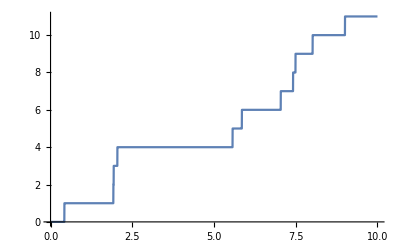

```mathematica
Plot[Piecewise[path],{u,0,10}]
```

```mathematica
??DisplayFunction
```

DisplayFunction is an option for graphics and sound functions that specifies a function to apply to graphics and sound objects before returning them.

Attributes[DisplayFunction]={Protected}

```mathematica
Table[g[u_]:=i-1/;s[[i]]≤u<s[[i+1]],{i,1,Num+1}];
```

```mathematica
graph2=Table[Plot[g[u],{u,s[[i]],s[[i+1]]},PlotRange->{{0,s[[Num+1]]+1},{0,Num+1}},DisplayFunction->Identity],{i,1,Num+1}];
```

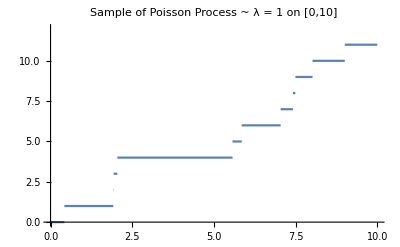

```mathematica
Show[graph2,PlotLabel->"Sample of Poisson Process ~ λ = 1  on  [0,10]",DisplayFunction->$DisplayFunction]
```

Generate a sample of size n for Poisson Process on [0, t]

```mathematica
Clear[a,s,t,r,λ,m,n];  n=1000;λ=2;t=10;m={};   
Do[a=0;s=0;Label[start];r=Random[ExponentialDistribution[λ]]; s=s+r;  If[s≤t,a=a+1;Goto[start]];AppendTo[m,a],{n}]
```

```mathematica
Mean[m]//N
```

19.976

```mathematica
Variance[m]//N
```

19.531

Compare sample results with exact values corresponding to Poisson Process

```mathematica
n=10000;λ=2;t=10;m={};   
Do[a=0;s=0;Label[start];r=Random[ExponentialDistribution[λ]]; s=s+r;  If[s≤t,a=a+1;Goto[start]];AppendTo[m,a],{n}]
Print[" sample mean  = ",  Mean[m]//N,  "   EN(t) = λt = ",λ t]
Print[" sample variance  = ",  Variance[m]//N,  "  VarN(t) = λt = ",λ t]
```

sample mean  = 20.0052   EN(t) = λt = 20

sample variance  = 20.389  VarN(t) = λt = 20

The waiting time for the n-th arrival,  S_n= X_1 +...+ X_n = τ_n where  X_i= S_i - S_(i-1)  (S_0= 0)  are independent exponential random variables with parameter  λ ,  has Gamma distribution with parameters (n, λ).  Here  X_i has density f(x) =  λe^(-λ x), x > 0,  
E X_i= 1/λ,  Var X_i= 1/λ^2.   Then  E S_n = n 1/λ  and  Var S_n= n1/λ^2.

Generate a random sample for  n = 10,  λ = 2. The data simulated below, in agreement with E S_10 = 5  and Var S_10= 2.5

```mathematica
S10:=Apply[Plus,Table[Random[ExponentialDistribution[2]],{10}]]
```

```mathematica
S10
```

8.12684

```mathematica
Sample[n_]:=Table[S10,{n}]
```

```mathematica
data=Sample[1000];
```

```mathematica
Mean[data]
```

4.95353

```mathematica
Variance[data]
```

2.5021

Generate ordered random sample (from smallest to largest)

```mathematica
Sort[{4.5,1.2,.7,2.3}]                  (* orders elements from smallest to largest *)
```

{0.7,1.2,2.3,4.5}

```mathematica
sample2=RandomReal[{0,1},10]
```

{0.503527,0.533028,0.676368,0.0729684,0.346227,0.0301065,0.80585,0.312665,0.676508,0.42244}

```mathematica
Sort[sample2]                                (* ordered sample2 *)
```

{0.0301065,0.0729684,0.312665,0.346227,0.42244,0.503527,0.533028,0.676368,0.676508,0.80585}

```mathematica
a={{1,1},{3,3},{5,5}};b={{2,4},{4,8}};
```

Plot Option:               PlotRange→{{a, b},{c, d}},     gives the graph window for  a ≤ x ≤ b,  c ≤ y ≤ d

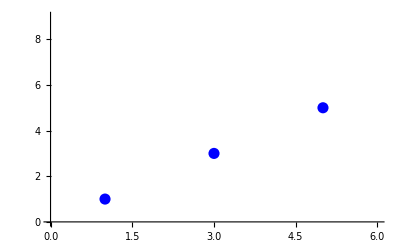

```mathematica
g1=ListPlot[a,PlotStyle->{Blue,PointSize[.02]},PlotRange->{{0,6},{0,9}}]
```

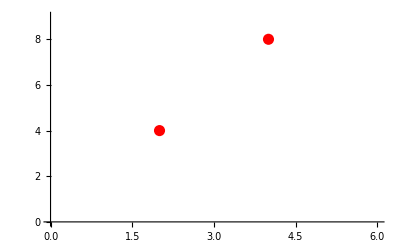

```mathematica
g2=ListPlot[b,PlotStyle->{Red,PointSize[.02]},PlotRange->{{0,6},{0,9}}]
```

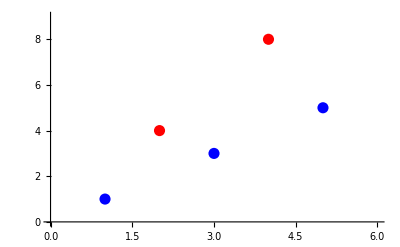

```mathematica
Show[g1,g2]                                             (*combined plot *)
```

```mathematica
?Union
"Union[list1, list2, ... ] gives a sorted list of all the distinct elements that appear in any of the listi. Union[list] gives a sorted version of a list, in which all duplicated elements have been dropped." More…
```

```mathematica
Clear[F,G,H,a,b,c]
```

```mathematica
F={a,b,c};G={a,b};H={a,b,c};
```

```mathematica
Union[F,{a}]               (* given lists A & B, Union[A,B] acts as A ∪ B *)
```

{a,b,c}

```mathematica
F==H
```

True

```mathematica
G==F
```

False

A game has 3 outcomes {Lose,  Draw, Win} ~ {-1,  0 , 1} with equal chances of  1/3 .  Play until all 3 outcomes occur

```mathematica
Clear[Num,Sample,outcome]  (* {} stands for  empty and denoted by  *)
```

```mathematica
(Num=0;
Sample={};l={};Label[start];m=l;
outcome=RandomInteger[{-1,1}];
AppendTo[Sample,outcome];Num=Num+1;l=m∪{outcome};
If[l≠{-1,0,1},Goto[start]])
```

```mathematica
Sample
```

{3,2,3,2,1,5,4}

```mathematica
Num
```

12

To find the average of n samples use  Do[ . ] statement as follows

```mathematica
average[n_]:=(NumTotal=0;Do[Num=0;l={};Label[start];m=l;outcome=RandomInteger[{-1,1}];Num=Num+1;l=m∪{outcome};If[l≠{-1,0,1},Goto[start]];NumTotal=NumTotal+Num,{n}];N[NumTotal/n])
```

```mathematica
average[1000]
```

5.445

Exact value , as found in the coupon collecting model is

```mathematica
Clear[t]
```

```mathematica
exact=∫_0^∞ (1-(1-ⅇ^(-t/3))^3)ⅆt
```

11/2

```mathematica
exact//N
```

5.5

Suppose that a shock profile is a function  f(x) UnitStep(x)  where  f(x) > 0 and  lim_(x→∞) f(x) = 0.

```mathematica
?UnitStep
```

RowBox[{"UnitStep", "[", StyleBox["x", "TI"], "]"}] represents the unit step function, equal to 0 for RowBox[{"x", "<", "0"}] and 1 for RowBox[{"x", "≥", "0"}]. 
RowBox[{"UnitStep", "[", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "]"}] represents the multidimensional unit step function which is 1 only if none of the SubscriptBox["x", "i"] are negative.

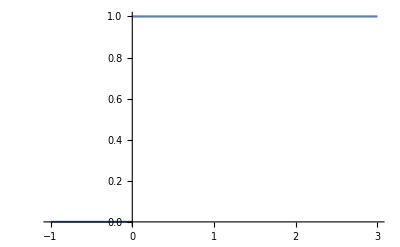

```mathematica
Plot[UnitStep[x],{x,-1,3}]
```

If  the shock arrives at time  s > 0  its  effect at time t is represented by  f(t-s) UnitStep(t-s)

```mathematica
Clear[f,u,s]
```

```mathematica
f[u_]:=1/(1+u^2)UnitStep[u];
```

f(t) describes the profile of the shock from arrival at time t = 0 forward. 

When a shock arrives at time t = s  we use  f(t-s)  = the translation of f(t) to the right by s.

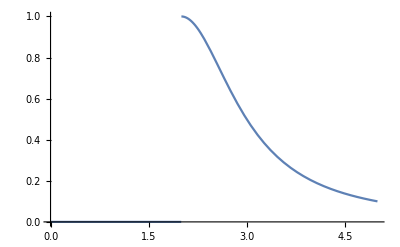

```mathematica
Plot[f[u-2],{u,0,5}]             (*  s=2,  0 ≤ u ≤ 5=t *)
```

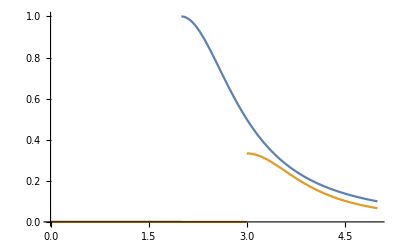

```mathematica
Plot[{f[u-2],1/3f[u-3]},{u,0,5}]     (*  s=2,  0 ≤ u ≤ 5=t, 2 shocks combined *)
```

If shocks arrive at times  0 <s_1 < s_2 < ... <  s_n <t  with amplitudes A[i],  then their total cumulative effect at time  t  is expressed by
 
shockTotal[t] = ∑_(i=1)^n A[i]*f[t-s_i],

```mathematica
s[1]=1;s[2]=2.6;s[3]=5.1; A[1]=1;A[2]=1.5;A [3]=.6;
shockTotal[u_]:=∑_(i=1)^3 A[i]*f[u-s[i]];
```

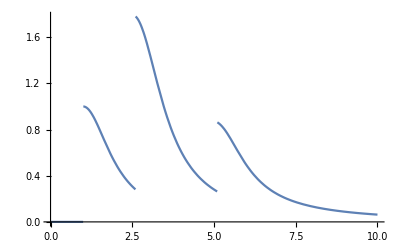

```mathematica
Plot[shockTotal[u],{u,0,10}]       (* cumulative at time *)
```

```mathematica
shockTotal[10]     (* cumulative effect at time t=10 *)
```

0.0630865

## Better illustration

```mathematica
(* individual effects combined , 0 ≤ u ≤ t = 10. *)
```

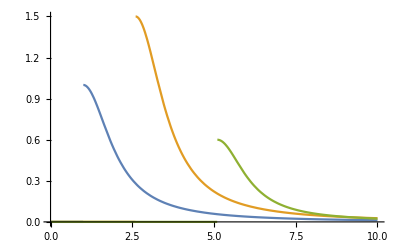

```mathematica
Plot[{A[1]*f[u-s[1]],A[2]*f[u-s[2]],A[3]*f[u-s[3]]},{u,0,10}, PlotRange->All]
```

Electronic Counter Model.  Generate amplitudes ~ U[1,3]

```mathematica
Clear[A,S,e2,totalA]
```

```mathematica
Num=5;
```

```mathematica
Table[A[i]=RandomReal[{1,3}],{i,1,Num}]
```

{2.02263,1.32115,1.15003,1.47406,2.05134}

Generate exponential interarrival times  ~   λ = 2  and assume dissipation rate α = 1.

```mathematica
λ=2; α=1;
```

```mathematica
e2=Table[Random[ExponentialDistribution[2]],{Num}]
```

{1.38408,0.533401,3.037,0.926179,0.0336303}

Below are Poisson arrival times  S_1<  S_2<  S_3<  S_4<  S_5

```mathematica
a=Table[S[i]=Delete[FoldList[Plus,0,e2],1][[i]],{i,1,Num}]
```

{1.38408,1.91748,4.95448,5.88066,5.91429}

```mathematica
T=Max[a]+1;    (* note that these arrivals occurred in interval [0,T] *)
```

The formula below shows the cumulative effect of shocks at time T, given Num= N (T) = # shocks that occured in [0, T].

```mathematica
totalA[t_]=∑_(i=1)^Num A[i] *ⅇ^(-α*(t- S[i]))*UnitStep[t- S[i]]
```

2.05134 ⅇ^(5.91429-t) UnitStep[-5.91429+t]+1.47406 ⅇ^(5.88066-t) UnitStep[-5.88066+t]+1.15003 ⅇ^(4.95448-t) UnitStep[-4.95448+t]+1.32115 ⅇ^(1.91748-t) UnitStep[-1.91748+t]+2.02263 ⅇ^(1.38408-t) UnitStep[-1.38408+t]

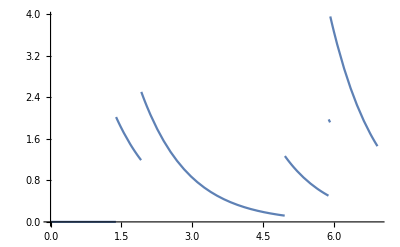

```mathematica
Plot[totalA[t],{t,0,T}]
```

```mathematica
f[u_]:=ⅇ^(-α*u) UnitStep[u]
```

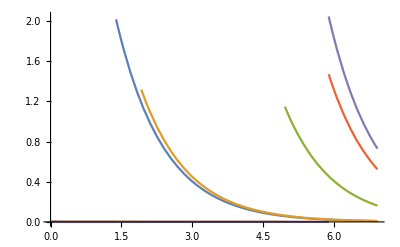

```mathematica
Plot[{A[1]*f[u-S[1]],A[2]*f[u-S[2]],A[3]*f[u-S[3]],A[4]*f[u-S[4]],A[5]*f[u-S[4]]},{u,0,T}, PlotRange->All]
```